```mathematica
Cv=0.93; Ca=0.75;
ℏ = 1.054571596 10^-27;c=2.99792458 10^10;m=9.10938188 10^-28; α=7.297352533 10^-3;
Gm= 1.16639 10^-5( 0.510998902 10^-3)^2;
```

```mathematica
Subscript[λ, e]= ℏ/(m c)
Subscript[τ, e] =Subscript[λ, e]/c
Subscript[E, e] = m c^2
Subscript[Q, e] = Subscript[E, e]/(Subscript[λ, e]^3 Subscript[τ, e])
```

3.86159×10^-11

1.28809×10^-21

8.1871×10^-7

1.10379×10^46

```mathematica
η[T_]:=(1.380649*10^-16 T)/(m c^2);
η[10^9]
```

0.168637

```mathematica
x[ρ6_]:=(1.009^3*100ρ6)/(3*4.41);
z[ρ6_]:=1.34*100/((1+x[ρ6]^2)^0.5);
μ[ρ6_]:=(1+x[ρ6]^2)^0.5;
vF[ρ6_]:=(1-μ[ρ6]^-2)^0.5;
ω[ρ6_]:=((2α 100 vF[ρ6])/(4.41π))^0.5;
```

```mathematica
RR00[x_]:=1+12.306728780393993/x^(1/2)+159.28494555577515/x^(3/2)+866.7067019290372/x^(5/2)+4511.652667090261/x^(7/2)+10960.54437176578/x^(9/2)+20170.404437273137/x^(11/2)+16575.589106915428/x^(13/2)+2991.9346396672163/x^(15/2);
Qb[ρ6_]:=(Subscript[Q, e] Gm^2 α(Cv+Ca))/(576(2π)^(11/2))*100/4.41 μ[ρ6]^-6*(0.168637)^(3/2)ω[ρ6]^(15/2)Exp[(-ω[ρ6])/0.168637]RR00[ω[ρ6]/(2*0.168637)];
```

```mathematica
D1[ρ6_]:=1+0.4228z[ρ6]+0.1014 z[ρ6]^2+0.006240 z[ρ6]^3;
D2[ρ6_]:=1+0.4535 z[ρ6]^(2/3)+0.03008z[ρ6]-0.05043 z[ρ6]^2+0.004314 z[ρ6]^3;
Qbc[ρ6_]:=9.04*10^20 D1[ρ6] D2[ρ6] Exp[(-z[ρ6])/2];
```

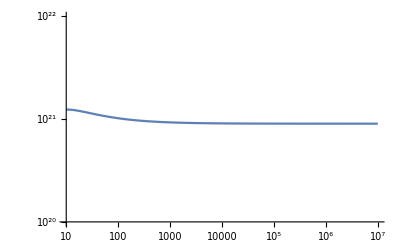

```mathematica
LogLogPlot[Qbc[ρ6],{ρ6,10,10^7},PlotRange->{{10,10^7},{10^20,10^22}}]
```

```mathematica
LogLogPlot[{Qb[ρ6],Qbc[ρ6]},{ρ6,10,1000},PlotRange->{{10,1000},{10,10^30}},Frame->True,RotateLabel->False,FrameLabel->{ρ6,Q},LabelStyle->Directive[FontFamily->"Times",FontSize->18, Black,Thin],PlotLabels->{"Qsync","Q_(eγ → eνν)"}]
```

```mathematica
Qb[0.11]
```

3.01295×10^9

```mathematica
QIII[B_,T_,ρ6_]:=8/9 1.023*10^23*1.678(B/(4.41*10^13))^3(2π)^-3(1-9/(4Exp[1]))((2B)/(4.41*10^13))^(1/4)Exp[(-5.93*10^9)/T((2B)/(4.41*10^13))^0.5] B/(4.41*10^13(2π)^2)1.009(ρ6/2)^(1/3);
```

```mathematica
Q[ρ6_]:=QIII[10^15,10^9,ρ6];
```

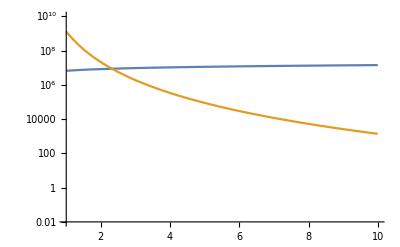

```mathematica
LogPlot[{Q[ρ6],Qb[ρ6]},{ρ6,1,10},PlotRange->{{1,10},{0.01,10^10}}]
```

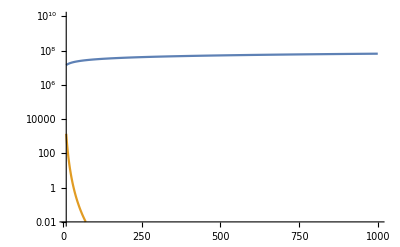

```mathematica
LogPlot[{Q[ρ6],Qb[ρ6]},{ρ6,10,1000},PlotRange->{{10,1000},{0.01,10^10}}]
```